```mathematica
(*This just rewrites a whole mess of variables from a Mathematica notation to a Matlab notation*)
varreplace=Flatten@{{Nx[x,y,z]->Nx,Ny[x,y,z]->Ny,Nz[x,y,z]->Nz,Table[D[Nx[x,y,z],{x,y,z}⟦ii⟧]->ToExpression["dNxd"<>ToString[{x,y,z}⟦ii⟧]],{ii,3}],
Table[D[Ny[x,y,z],{x,y,z}⟦ii⟧]->ToExpression["dNyd"<>ToString[{x,y,z}⟦ii⟧]],{ii,3}],
Table[D[Nz[x,y,z],{x,y,z}⟦ii⟧]->ToExpression["dNzd"<>ToString[{x,y,z}⟦ii⟧]],{ii,3}],Table[D[Nx[x,y,z],{x,y,z}⟦ii⟧,{x,y,z}⟦jj⟧]->ToExpression["d2Nxd"<>ToString[{x,y,z}⟦ii⟧]<>"d"<>ToString[{x,y,z}⟦jj⟧]],{ii,3},{jj,3}],Table[D[Ny[x,y,z],{x,y,z}⟦ii⟧,{x,y,z}⟦jj⟧]->ToExpression["d2Nyd"<>ToString[{x,y,z}⟦ii⟧]<>"d"<>ToString[{x,y,z}⟦jj⟧]],{ii,3},{jj,3}],Table[D[Nz[x,y,z],{x,y,z}⟦ii⟧,{x,y,z}⟦jj⟧]->ToExpression["d2Nzd"<>ToString[{x,y,z}⟦ii⟧]<>"d"<>ToString[{x,y,z}⟦jj⟧]],{ii,3},{jj,3}]},{Nx[x,y]->Nx,Ny[x,y]->Ny,Table[D[Nx[x,y],{x,y}⟦ii⟧]->ToExpression["dNxd"<>ToString[{x,y}⟦ii⟧]],{ii,2}],
Table[D[Ny[x,y],{x,y}⟦ii⟧]->ToExpression["dNyd"<>ToString[{x,y}⟦ii⟧]],{ii,2}],Table[D[Nx[x,y],{x,y}⟦ii⟧,{x,y}⟦jj⟧]->ToExpression["d2Nxd"<>ToString[{x,y}⟦ii⟧]<>"d"<>ToString[{x,y}⟦jj⟧]],{ii,2},{jj,2}],Table[D[Ny[x,y],{x,y}⟦ii⟧,{x,y}⟦jj⟧]->ToExpression["d2Nyd"<>ToString[{x,y}⟦ii⟧]<>"d"<>ToString[{x,y}⟦jj⟧]],{ii,2},{jj,2}]},Flatten@{θ[x,y,z]->θ,ϕ[x,y,z]->ϕ,Table[D[θ[x,y,z],{x,y,z}⟦ii⟧]->ToExpression["dθd"<>ToString[{x,y,z}⟦ii⟧]],{ii,3}],
Table[D[ϕ[x,y,z],{x,y,z}⟦ii⟧]->ToExpression["dϕd"<>ToString[{x,y,z}⟦ii⟧]],{ii,3}],
Table[D[θ[x,y,z],{x,y,z}⟦ii⟧,{x,y,z}⟦jj⟧]->ToExpression["d2θd"<>ToString[{x,y,z}⟦ii⟧]<>"d"<>ToString[{x,y,z}⟦jj⟧]],{ii,3},{jj,3}],Table[D[ϕ[x,y,z],{x,y,z}⟦ii⟧,{x,y,z}⟦jj⟧]->ToExpression["d2ϕd"<>ToString[{x,y,z}⟦ii⟧]<>"d"<>ToString[{x,y,z}⟦jj⟧]],{ii,3},{jj,3}]},Flatten@{ϕ[x,y]->ϕ,
Table[D[ϕ[x,y],{x,y}⟦ii⟧]->ToExpression["dϕd"<>ToString[{x,y}⟦ii⟧]],{ii,2}],
Table[D[ϕ[x,y],{x,y}⟦ii⟧,{x,y}⟦jj⟧]->ToExpression["d2ϕd"<>ToString[{x,y}⟦ii⟧]<>"d"<>ToString[{x,y}⟦jj⟧]],{ii,2},{jj,2}]}};
```

Director:

```mathematica
(*A few options here. Uncomment your chouce and evaluate the whole notebook. It may take a while for the 3D cases, especially with saddlesplay.*)
(*3D Cartesian:*)
(*n:={Nx[x,y,z],Ny[x,y,z],Nz[x,y,z]}
vars:={Nx[x,y,z],Ny[x,y,z],Nz[x,y,z]}*)
(*2D Cartesian*)
(*n:={Nx[x,y],Ny[x,y],0}
vars:={Nx[x,y],Ny[x,y]}*)
(*3D Spherical*)
(*n:={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}/.{θ->θ[x,y,z],ϕ->ϕ[x,y,z]}
vars:={θ[x,y,z],ϕ[x,y,z]}*)
(*2D Polar*)
n:={Cos[ϕ],Sin[ϕ],0}/.{ϕ->ϕ[x,y]}
vars:={ϕ[x,y]}
```

Levi-civita tensor:

```mathematica
ϵ=Normal@LeviCivitaTensor[3];
```

Equations 4 & 5. Q with 2 arguments will form the components of the Q-tensor, and Q with 3 arguments will take the derivative of an element of the Q tensor with respect to a variable.

```mathematica
Q[j_,k_]:=S/2(3 n⟦j⟧n⟦k⟧-KroneckerDelta[j,k])
Q[j_,k_,l_]:=D[Q[j,k],{x,y,z}⟦l⟧]
```

Equation 3. Einstein summation notation means that the repeated indices are summed over. For now, we will not need G_3^(2) (which contains the saddle-splay term) or G_4^(2) (which accounts for cholesteric pitch). However, we will need G_3^(2) when it comes time to encode weak boundaries!

```mathematica
G12=Sum[Q[j,k,l]Q[j,k,l],{j,3},{k,3},{l,3}]//Simplify;
G22=Sum[Q[j,k,k]Q[j,l,l],{j,3},{k,3},{l,3}]//Simplify;
G32=Sum[Q[j,k,l]Q[j,l,k],{j,3},{k,3},{l,3}]//Simplify;
G42=Sum[ϵ⟦j,k,l⟧Q[j,m]Q[k,m,l],{j,3},{k,3},{l,3},{m,3}]//Simplify;
G63=Sum[Q[j,k]Q[l,m,j]Q[l,m,k],{j,3},{k,3},{l,3},{m,3}]//Simplify;
```

Equaton 13 (we aren’t doing anything with electric fields, thankfully).

```mathematica
(*Note the K24 saddle-splay term. Multiply it by 0 if you don't want it.*)
fgQ=Collect[Simplify[1/27(K33-K11+3K22)G12/S^2+2/9(K11-K22-0*K24)G22/S^2+2/9 G32/S^2+2/27(K33-K11)G63/S^3],{K11,K22,K33},Simplify];
```

```mathematica
bend:=1/2 K11 Div[n,{x,y,z}]^2//FullSimplify
twist:=1/2 K22(n.Curl[n,{x,y,z}])^2//FullSimplify
splay:=1/2 K33(Cross[n,Curl[n,{x,y,z}]].Cross[n,Curl[n,{x,y,z}]])//Simplify
(*Del={D[#,x],D[#,y],D[#,z]}&;
saddlesplay:=1/2 K24 Div[(n.Del[#]&)@n-n(Div[n,{x,y,z}]),{x,y,z}]//FullSimplify*)
saddlesplay=0;
(*Comment the saddle-splay back in if you choose.*)
fgOF=bend+twist+splay+saddlesplay;
```

```mathematica
(*Pick which form of the free energy to use, including the surface energy if you so choose (scaled by factor Ws). The surface energy applies an energy bonus for aligned with the preferred direction notated by the unit vector {Bx,By,Bz}. Feel free to define this in spherical coordinates or whatever.*)
fgS=-Ws ({Bx,By,Bz}.n)^2;


(*use this line to switch between Oseen Frank and Q tensor representations*)
fg=fgOF(*+fgS*) 
(*fg = fgQ;*)
```

```mathematica
1/2 K33 (Sin[ϕ[x,y]] Derivative[0,1][ϕ][x,y]+Cos[ϕ[x,y]] Derivative[1,0][ϕ][x,y])^2+1/2 K11 (Cos[ϕ[x,y]] Derivative[0,1][ϕ][x,y]-Sin[ϕ[x,y]] Derivative[1,0][ϕ][x,y])^2/.varreplace//ToMatlab
```

(1/2).*K11.*(dϕdy.*cos(ϕ)+(-1).*dϕdx.*sin(ϕ)).^2+(1/2).*K33.*( ...
  dϕdx.*cos(ϕ)+dϕdy.*sin(ϕ)).^2;

```mathematica
(*General form for Euler-Lagrange equations. Notice the intermittent Simplify's. This is a little quicker than doing it all at the end.*)
ELeqs=Flatten@Table[
D[fg,vars⟦ELii⟧]-Sum[Simplify@D[Simplify@Quiet@D[fg,Simplify@D[vars⟦ELii⟧,{x,y,z}⟦ii⟧]],{x,y,z}⟦ii⟧],{ii,3}],{ELii,Length@vars}];
```

```mathematica
ELeqsSimp=Collect[#,{K11,K22,K33,K24},Simplify]&/@ELeqs;
```

```mathematica
(*Download this package online.*)
<<ToMatlab`
```

```mathematica
(*You now have an array that has the Euler-Lagrange equation for each of your variables. Replace the number to view the EL equation for the corresponding variable.*)
vars
```

{ϕ[x,y]}

```mathematica
(*Check out the one constant approximation to see if it makes sense.*)
ELeqs/.{K11->5*^-12,K22->5*^-12,K33->5*^-12}
```

{-(Cos[ϕ[x,y]]^2/200000000000+Sin[ϕ[x,y]]^2/200000000000) ϕ^(0,2)[x,y]+((-Sin[ϕ[x,y]] ϕ^(0,1)[x,y]-Cos[ϕ[x,y]] ϕ^(1,0)[x,y]) (Cos[ϕ[x,y]] ϕ^(0,1)[x,y]-Sin[ϕ[x,y]] ϕ^(1,0)[x,y]))/200000000000+((Sin[ϕ[x,y]] ϕ^(0,1)[x,y]+Cos[ϕ[x,y]] ϕ^(1,0)[x,y]) (Cos[ϕ[x,y]] ϕ^(0,1)[x,y]-Sin[ϕ[x,y]] ϕ^(1,0)[x,y]))/200000000000-(Cos[ϕ[x,y]]^2/200000000000+Sin[ϕ[x,y]]^2/200000000000) ϕ^(2,0)[x,y]}

```mathematica
ELeqsSimp⟦1⟧/.varreplace//ToMatlab
```

(1/2).*K33.*((-2).*d2ϕdxdx.*cos(ϕ).^2+(-2).*dϕdx.*dϕdy.*cos(2.*ϕ)+ ...
  (-2).*d2ϕdydy.*sin(ϕ).^2+(-2).*d2ϕdxdy.*sin(2.*ϕ)+dϕdx.^2.*sin(2.* ...
  ϕ)+(-1).*dϕdy.^2.*sin(2.*ϕ))+(1/2).*K11.*(2.*dϕdx.*dϕdy.*cos(2.*ϕ) ...
  +(-2).*(d2ϕdydy.*cos(ϕ).^2+sin(ϕ).*((-2).*d2ϕdxdy.*cos(ϕ)+ ...
  dϕdx.^2.*cos(ϕ)+d2ϕdxdx.*sin(ϕ)))+dϕdy.^2.*sin(2.*ϕ));

```mathematica
(*In the 2D case with one constant approximation, the energy comes out linear. Mathematica has nice built in tools for solving such systems.*)
```

Show::gcomb: Could not combine the graphics objects in {GraphicsBox[List[GrayLevel[1], DiskBox[List[0, 0]]], Rule[Background, GrayLevel[0.85`]]], VectorPlot[Through[{Cos, Sin}[sol[x, y]]], {x, y} ∈ region, VectorStyle → Arrowheads[0]]}.

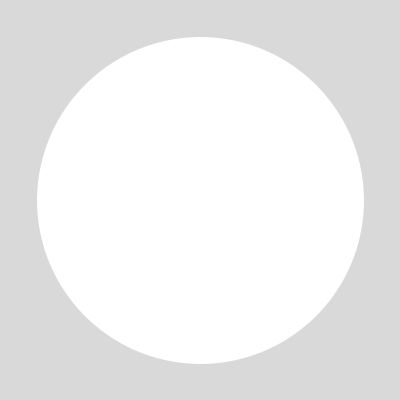
Show[{-Graphics-,VectorPlot[Through[{Cos,Sin}[sol[x,y]]],{x,y}∈region,VectorStyle→Arrowheads[0]]}]

```mathematica
(*For a circular region, it likes to put the singularity at an edge.*)
region=Disk[];
sol=NDSolveValue[{∇_{x,y}^2 ϕ[x,y]==0,DirichletCondition[ϕ[x,y]==ArcTan[x, y]+π/2,x^2+y^2==1]},ϕ,{x,y}∈region];
Show[{Graphics[{White,region},Background->LightGray],Quiet@VectorPlot[Through[{Cos,Sin}[sol[x,y]]],{x,y}∈region,VectorStyle->Arrowheads[0]]}]
```

Show::gcomb: Could not combine the graphics objects in {GraphicsBox[List[GrayLevel[1], RectangleBox[List[0, 0]]], Rule[Background, GrayLevel[0.85`]]], VectorPlot[Through[{Cos, Sin}[sol2[x, y]]], {x, y} ∈ region2, VectorStyle → Arrowheads[0]]}.

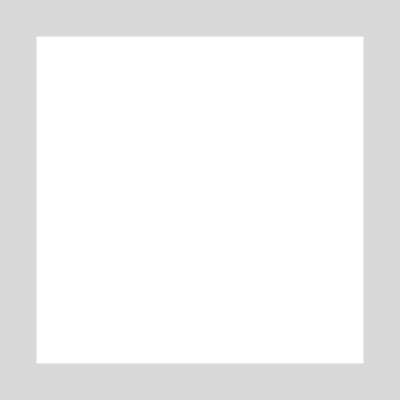
Show[{-Graphics-,VectorPlot[Through[{Cos,Sin}[sol2[x,y]]],{x,y}∈region2,VectorStyle→Arrowheads[0]]}]

```mathematica
(*Here's a linear twist.*)
region2=Rectangle[];
sol2=NDSolveValue[{∇_{x,y}^2 ϕ[x,y]==0,DirichletCondition[ϕ[x,y]==0,x==0],DirichletCondition[ϕ[x,y]==π/2,x==1]},ϕ,{x,y}∈region2];
Show[{Graphics[{White,region2},Background->LightGray],Quiet@VectorPlot[Through[{Cos,Sin}[sol2[x,y]]],{x,y}∈region2,VectorStyle->Arrowheads[0]]}]
```

```mathematica
Show[{-Graphics-,VectorPlot[Through[{Cos,Sin}[sol2[x,y]]],{x,y}∈region2,VectorStyle->Arrowheads[0]]}]
```

VectorPlot::pllim: Range specification {x, y} ∈ region2 is not of the form {x, xmin, xmax}.

Show::gcomb: Could not combine the graphics objects in {GraphicsBox[List[GrayLevel[1], RectangleBox[List[0, 0]]], Rule[Background, GrayLevel[0.85`]]], VectorPlot[Through[{Cos, Sin}[sol2[x, y]]], {x, y} ∈ region2, VectorStyle → Arrowheads[0]]}.

Show[{-Graphics-,VectorPlot[Through[{Cos,Sin}[sol2[x,y]]],{x,y}∈region2,VectorStyle→Arrowheads[0]]}]

```mathematica
Information[varreplace]
```

Global`varreplace

varreplace={Nx[x,y,z]→Nx,Ny[x,y,z]→Ny,Nz[x,y,z]→Nz,Nx^(1,0,0)[x,y,z]→dNxdx,Nx^(0,1,0)[x,y,z]→dNxdy,Nx^(0,0,1)[x,y,z]→dNxdz,Ny^(1,0,0)[x,y,z]→dNydx,Ny^(0,1,0)[x,y,z]→dNydy,Ny^(0,0,1)[x,y,z]→dNydz,Nz^(1,0,0)[x,y,z]→dNzdx,Nz^(0,1,0)[x,y,z]→dNzdy,Nz^(0,0,1)[x,y,z]→dNzdz,Nx^(2,0,0)[x,y,z]→d2Nxdxdx,Nx^(1,1,0)[x,y,z]→d2Nxdxdy,Nx^(1,0,1)[x,y,z]→d2Nxdxdz,Nx^(1,1,0)[x,y,z]→d2Nxdydx,Nx^(0,2,0)[x,y,z]→d2Nxdydy,Nx^(0,1,1)[x,y,z]→d2Nxdydz,Nx^(1,0,1)[x,y,z]→d2Nxdzdx,Nx^(0,1,1)[x,y,z]→d2Nxdzdy,Nx^(0,0,2)[x,y,z]→d2Nxdzdz,Ny^(2,0,0)[x,y,z]→d2Nydxdx,Ny^(1,1,0)[x,y,z]→d2Nydxdy,Ny^(1,0,1)[x,y,z]→d2Nydxdz,Ny^(1,1,0)[x,y,z]→d2Nydydx,Ny^(0,2,0)[x,y,z]→d2Nydydy,Ny^(0,1,1)[x,y,z]→d2Nydydz,Ny^(1,0,1)[x,y,z]→d2Nydzdx,Ny^(0,1,1)[x,y,z]→d2Nydzdy,Ny^(0,0,2)[x,y,z]→d2Nydzdz,Nz^(2,0,0)[x,y,z]→d2Nzdxdx,Nz^(1,1,0)[x,y,z]→d2Nzdxdy,Nz^(1,0,1)[x,y,z]→d2Nzdxdz,Nz^(1,1,0)[x,y,z]→d2Nzdydx,Nz^(0,2,0)[x,y,z]→d2Nzdydy,Nz^(0,1,1)[x,y,z]→d2Nzdydz,Nz^(1,0,1)[x,y,z]→d2Nzdzdx,Nz^(0,1,1)[x,y,z]→d2Nzdzdy,Nz^(0,0,2)[x,y,z]→d2Nzdzdz,Nx[x,y]→Nx,Ny[x,y]→Ny,Nx^(1,0)[x,y]→dNxdx,Nx^(0,1)[x,y]→dNxdy,Ny^(1,0)[x,y]→dNydx,Ny^(0,1)[x,y]→dNydy,Nx^(2,0)[x,y]→d2Nxdxdx,Nx^(1,1)[x,y]→d2Nxdxdy,Nx^(1,1)[x,y]→d2Nxdydx,Nx^(0,2)[x,y]→d2Nxdydy,Ny^(2,0)[x,y]→d2Nydxdx,Ny^(1,1)[x,y]→d2Nydxdy,Ny^(1,1)[x,y]→d2Nydydx,Ny^(0,2)[x,y]→d2Nydydy,θ[x,y,z]→θ,ϕ[x,y,z]→ϕ,θ^(1,0,0)[x,y,z]→dθdx,θ^(0,1,0)[x,y,z]→dθdy,θ^(0,0,1)[x,y,z]→dθdz,ϕ^(1,0,0)[x,y,z]→dϕdx,ϕ^(0,1,0)[x,y,z]→dϕdy,ϕ^(0,0,1)[x,y,z]→dϕdz,θ^(2,0,0)[x,y,z]→d2θdxdx,θ^(1,1,0)[x,y,z]→d2θdxdy,θ^(1,0,1)[x,y,z]→d2θdxdz,θ^(1,1,0)[x,y,z]→d2θdydx,θ^(0,2,0)[x,y,z]→d2θdydy,θ^(0,1,1)[x,y,z]→d2θdydz,θ^(1,0,1)[x,y,z]→d2θdzdx,θ^(0,1,1)[x,y,z]→d2θdzdy,θ^(0,0,2)[x,y,z]→d2θdzdz,ϕ^(2,0,0)[x,y,z]→d2ϕdxdx,ϕ^(1,1,0)[x,y,z]→d2ϕdxdy,ϕ^(1,0,1)[x,y,z]→d2ϕdxdz,ϕ^(1,1,0)[x,y,z]→d2ϕdydx,ϕ^(0,2,0)[x,y,z]→d2ϕdydy,ϕ^(0,1,1)[x,y,z]→d2ϕdydz,ϕ^(1,0,1)[x,y,z]→d2ϕdzdx,ϕ^(0,1,1)[x,y,z]→d2ϕdzdy,ϕ^(0,0,2)[x,y,z]→d2ϕdzdz,ϕ[x,y]→ϕ,ϕ^(1,0)[x,y]→dϕdx,ϕ^(0,1)[x,y]→dϕdy,ϕ^(2,0)[x,y]→d2ϕdxdx,ϕ^(1,1)[x,y]→d2ϕdxdy,ϕ^(1,1)[x,y]→d2ϕdydx,ϕ^(0,2)[x,y]→d2ϕdydy}